#### Death Rate Allometry

```mathematica
(*From Damuth 1982*)
```

```mathematica
(m^(-.3)/10^(1.67))
1/%
```

0.0213796/m^0.3

46.7735 m^0.3

```mathematica
10^(-.3*Log[10,x]-1.67)
```

0.0213796/x^0.3

```mathematica
texp[Masym_]:=46.77351412871981*Masym^(.30)/365
```

```mathematica
46.77351412871981*(Masym)^(.30)/365
```

0.128147 Masym^0.3

```mathematica
texp[1000]
1.02*1^.3

texp[1]
1.02*(1/1000)^.3
```

1.0179

1.02

0.128147

0.12841

```mathematica
texp[Masym_]:=46.77351412871981*Masym^(.30)*24*3600(*takes mass in grams returns seconds*)
```

```mathematica
texp[m]
```

4.04123×10^6 m^0.3

```mathematica
1.02*(m/1000)^.3*365*24*3600
```

4.04955×10^6 m^0.3

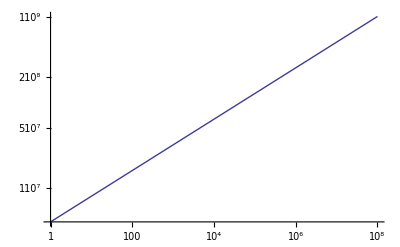

```mathematica
LogLogPlot[texp[x],{x,1,10^8},PlotRange->All]
```

```mathematica
q0[Masym_]:=.0124*(Masym/1000)^(-.56)/365/24/3600(*takes in grams returns seconds*)
α[Masym_]:=.709*(Masym/1000)^(-.27)/365/24/3600(*takes in grams returns seconds*)
```

```mathematica
texp[M]
q0[M]
α[M]
```

4.04123×10^6 M^0.3

(1.88198×10^-8)/M^0.56

(1.45158×10^-7)/M^0.27

```mathematica
deathcurve[n0_,Masym_,t_]:=n0*E^((q0[Masym]/α[Masym])*(1-E^(α[Masym]*t)))
```

```mathematica
deathcurve[100,1,1]
```

100.

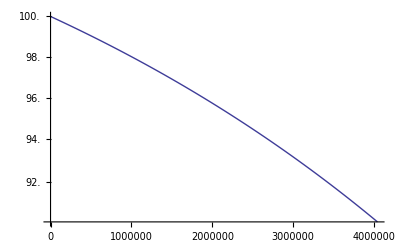

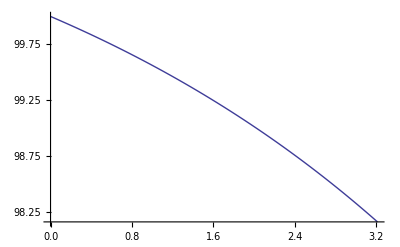

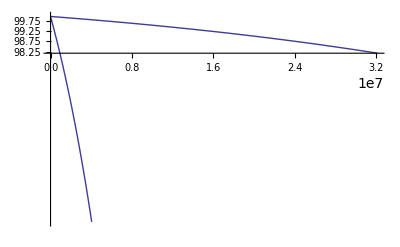

```mathematica
LogPlot[deathcurve[100,1,t],{t,0,texp[1]}]
LogPlot[deathcurve[100,1000,t],{t,0,texp[1000]}]
Show[{%,%%},PlotRange->All]
```

```mathematica
n=n0*E^((q/a)*(1-E^(a*t)))/m
```

(ⅇ^(((1-ⅇ^(a t)) q)/a) n0)/m

```mathematica
specificrate=FullSimplify[D[n,t]/n]
```

-ⅇ^(a t) q

```mathematica
FullSimplify[specificrate*n/D[n,t]]
```

1

```mathematica
specificratefn[Masym_,t_]:=E^(α[Masym]*t)*q0[Masym](*ignoring the minus sign*)
```

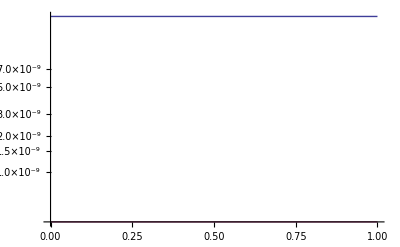

```mathematica
LogPlot[{specificratefn[1,t],specificratefn[1000,t]},{t,0,1},PlotRange->All]
```

```mathematica
FullSimplify[(1/tmax)*Integrate[E^(α*t)*q,{t,0,tmax}]]
```

((-1+ⅇ^(tmax α)) q)/(tmax α)

```mathematica
FullSimplify[(1/texp[Masym])*Integrate[specificratefn[Masym,t],{t,0,texp[Masym]}]]
```

(-3.2082×10^-8+3.2082×10^-8 ⅇ^(0.586615 Masym^0.03))/Masym^0.59

```mathematica
avedeathrate[Masym_]:=(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 Masym^0.02999999999999997))/Masym^0.5900000000000001
```

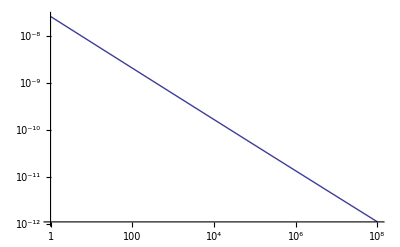

```mathematica
LogLogPlot[avedeathrate[x],{x,1,10^8},PlotRange->{All,All}]
```

```mathematica
avedeathrate[10^8]/avedeathrate[1]
```

0.0000423076

```mathematica
tmax=a2*M^(b2)
```

a2 M^b2

```mathematica
q=a0*(M)^(-b0)
α=a1*(M)^(-b1)
```

a0 M^-b0

a1 M^-b1

```mathematica
((-1+ⅇ^(tmax α)) q)/(tmax α)
```

(a0 (-1+ⅇ^(a1 a2 M^(-b1+b2))) M^(-b0+b1-b2))/(a1 a2)

```mathematica
FullSimplify[(1/tmax)*Integrate[E^(α*t)*q,{t,0,tmax}]]
```

(a2 (-1+ⅇ^(a1 M^b1 α)) M^(-b1-b2))/(a1 α)

#### Damuth’s law predicionts with a variable death rate

```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final_CPK_Variations/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
avedeathrate[Masym_]:=(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 Masym^0.02999999999999997))/Masym^0.5900000000000001
```

```mathematica
avedeathrate[M]
```

(-3.2082×10^-8+3.2082×10^-8 ⅇ^(0.586615 M^0.03))/M^0.59

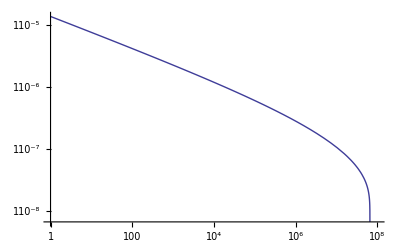

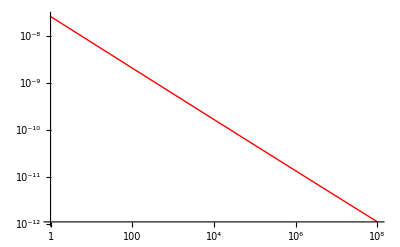

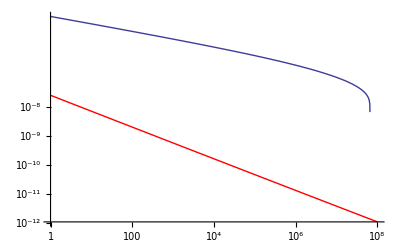

```mathematica
LogLogPlot[Mortality,{M,1,10^8}]
LogLogPlot[(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001,{M,1,10^8},PlotStyle->Red]
Show[{%,%%},PlotRange->All]
```

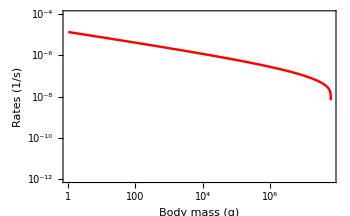

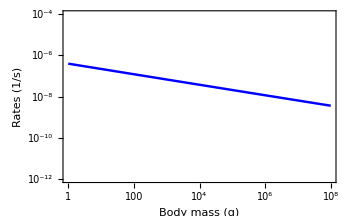

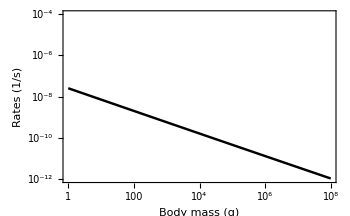

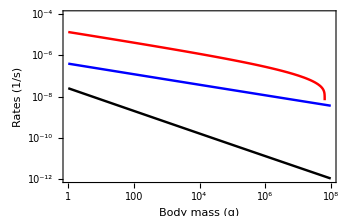

```mathematica
LogLogPlot[Mortality,{M,1,10^8},PlotStyle->{Red,Thickness[.005]},Frame->{True,True,False,False},FrameLabel->{Style["Body mass (g)",16],Style["Rates (1/s)",16]},Axes->False,LabelStyle->Directive[16],ImageSize->350,PlotRange->{All,{10^(-12),10^(-4)}}]
LogLogPlot[ConsumerGrowth,{M,1,10^8},PlotStyle->{Blue,Thickness[.005]},Frame->{True,True,False,False},FrameLabel->{Style["Body mass (g)",16],Style["Rates (1/s)",16]},Axes->False,LabelStyle->Directive[16],ImageSize->350,PlotRange->{All,{10^(-12),10^(-4)}}]
LogLogPlot[(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001,{M,1,10^8},PlotStyle->{Black,Thickness[.005]},Frame->{True,True,False,False},FrameLabel->{Style["Body mass (g)",16],Style["Rates (1/s)",16]},Axes->False,LabelStyle->Directive[16],ImageSize->350,PlotRange->{All,{10^(-12),10^(-4)}}]
outplt=Show[{%,%%,%%%}]
```

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
Export["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/NatureComm_REVISION/mortality-rate-comparison.eps",outplt]
```

/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/NatureComm_REVISION/mortality-rate-comparison.eps

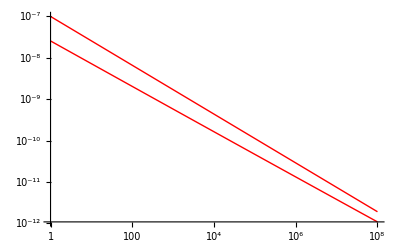

```mathematica
LogLogPlot[{(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001,.0000001/M^0.5900000000000001},{M,1,10^8},PlotStyle->Red]
```

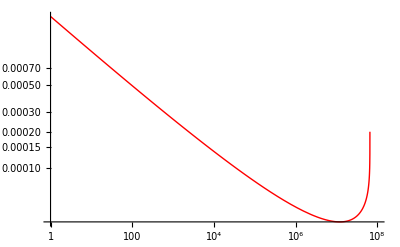

```mathematica
LogLogPlot[((-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001)/Mortality,{M,1,10^8},PlotStyle->Red]
```

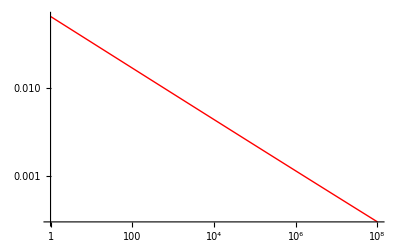

```mathematica
LogLogPlot[((-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001)/ConsumerGrowth,{M,1,10^8},PlotStyle->Red]
```

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->(ConsumerGrowth-(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001),μ->(Mortality-(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001),β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

```mathematica
RSS
```

(μ (-λ+σ))/(2 λ ρ+μ σ)

```mathematica
dimH/.{i->.01,M->10^5}
```

0.00199235

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"];
```

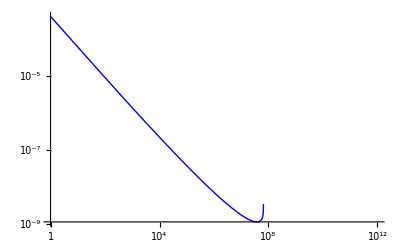

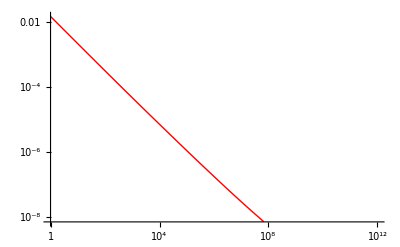

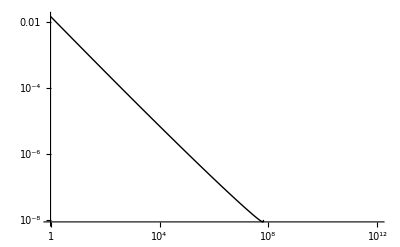

```mathematica
hplt=LogLogPlot[dimH/M,{M,1,10^12},PlotStyle->Blue]
fplt=LogLogPlot[dimF/M,{M,1,10^12},PlotStyle->Red]
fhplt=LogLogPlot[(dimH+dimF)/M,{M,1,10^12},PlotStyle->Black]
```

```mathematica
0.0115643*M^(-0.776818)
```

0.0115643/M^0.776818

```mathematica
dataplt=ListLogLogPlot[data,PlotRange->{{1,10^12},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}];
```

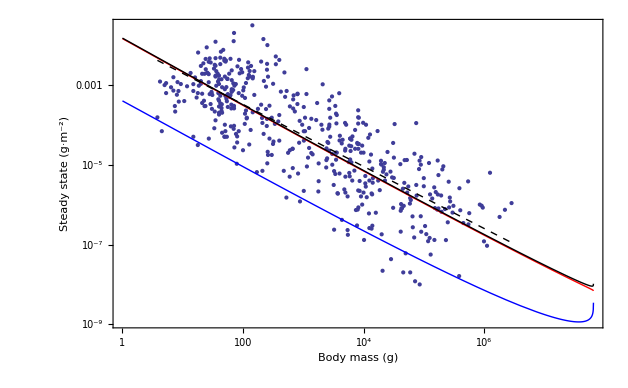

```mathematica
Show[dataplt,fplt,hplt,fhplt,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],PlotRange->All]
```

```mathematica
?NSolve
```

RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to find numerical approximations to the solutions of the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["Reals", "TI"]}], "]"}] finds solutions over the domain of real numbers.

```mathematica
NMinimize[{Mortality,7*10^7>M>10^7},M]
```

NMinimize::nrnum: The function value 1.14512×10^-8 + 9.36806×10^-9\ ⅈ is not a real number at {M} = {7.×10^7}.

NMinimize[{1/(148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]),70000000>M>10000000},M]

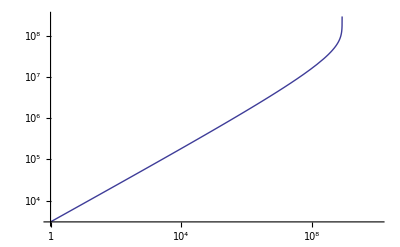

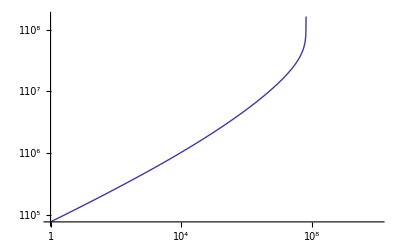

```mathematica
LogLogPlot[τSig,{M,1,10^10}]
LogLogPlot[-M^(1/4)/aprime*Log[ϵMu],{M,1,10^10}]
```

```mathematica
NSolve[f0*M^(γ-1)+mm0*M^(ζ-1)==1,M][[1]]
```

{M→6.53794×10^7}

```mathematica
Mortality/.{M->(1+10^(-14))*6.537941407352244*^7}
(Mortality-(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001)/.{M->(1+10^(-14))*6.537941407352244*^7}
```

2.15322×10^-9+1.96696×10^-10 ⅈ

2.15186×10^-9+1.96696×10^-10 ⅈ

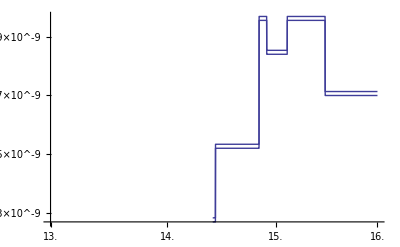

```mathematica
LogLogPlot[{Mortality,(Mortality-(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001)}/.{M->(1+10^(-x))*6.537941407352244*^7},{x,13,16}]
```

```mathematica
Table[(Mortality/(Mortality-(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001))/.{M->(1+10^(-x))*6.537941407352244*^7},{x,13,16,.1}]
```

{1.00057-0.0000574397 ⅈ,1.00057-0.0000574402 ⅈ,1.00058-0.0000574408 ⅈ,1.00058-0.0000574413 ⅈ,1.00059-0.0000574418 ⅈ,1.00059-0.0000574424 ⅈ,1.0006-0.0000574429 ⅈ,1.0006-0.0000574436 ⅈ,1.00061-0.0000574442 ⅈ,1.00062-0.0000574451 ⅈ,1.00063-0.0000574465 ⅈ,1.00063-0.0000574465 ⅈ,1.00064-0.000057448 ⅈ,Indeterminate,Indeterminate,1.00063,1.00064,1.00063,1.00063,1.00062,1.00062,1.00062,1.00062,1.00062,1.00062,1.00063,1.00063,1.00063,1.00063,1.00063,1.00063}

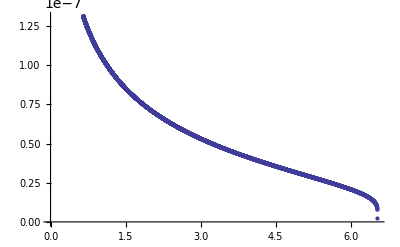

{6.53794×10^7,2.17119×10^-9}

```mathematica
miner=Table[{M,Mortality}/.{M->(10^(x))*6.537941407352244*^7},{x,-1,1,.0001}];
ListPlot[miner]
Last[Select[miner,Im[#[[2]]]==0&]]
```

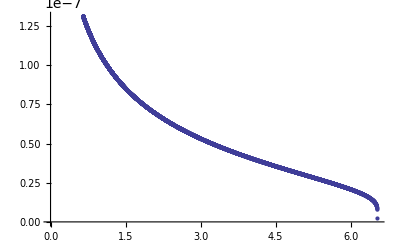

{6.53794×10^7,2.16982×10^-9}

```mathematica
miner=Table[{M,(Mortality-(-3.208202016813883*^-8+3.208202016813883*^-8 ⅇ^(0.5866152793876792 M^0.02999999999999997))/M^0.5900000000000001)}/.{M->(10^(x))*6.537941407352244*^7},{x,-1,1,.0001}];
ListPlot[miner]
Last[Select[miner,Im[#[[2]]]==0&]]
```

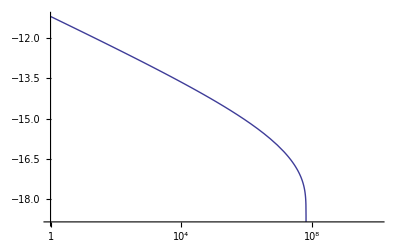

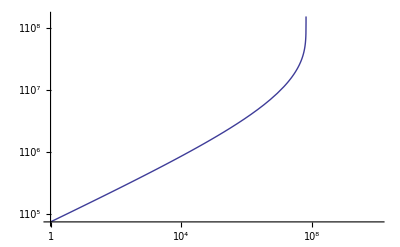

```mathematica
LogLinearPlot[Log[Mortality] ,{M,1,10^10}]
LogLogPlot[τMu ,{M,1,10^10}]
```

```mathematica
Hvariations={};
Fvariations={};
Do[

Hforplt=dimH/.{i->j};
Fforplt=dimF/.{i->j};


Hvariations=Append[Hvariations,LogLogPlot[Hforplt/M,{M,1,10^12},PlotStyle->Hue[j/.2]]];
Fvariations=Append[Fvariations,LogLogPlot[Fforplt/M,{M,1,10^12},PlotStyle->Hue[j/.2]]]
,
{j,-.05,.05,.0025}
]
```

```mathematica
dataplt=ListLogLogPlot[data,PlotRange->{{1,10^12},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}];
```

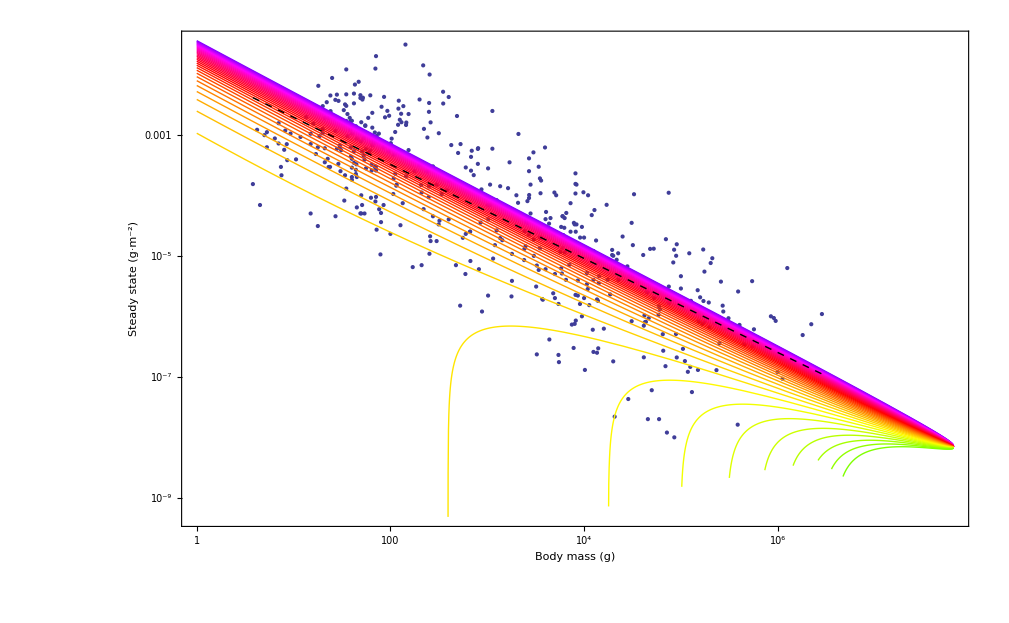

```mathematica
Show[dataplt,Fvariations,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],PlotRange->All]
```

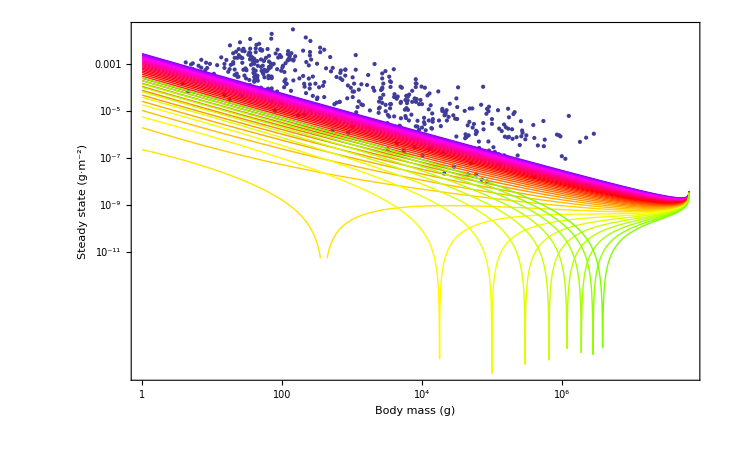

```mathematica
Show[dataplt,Hvariations,PlotRange->All]
```

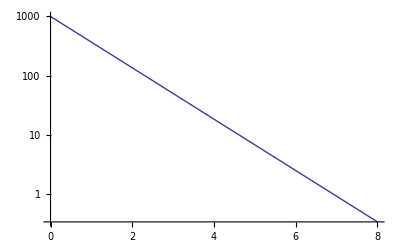

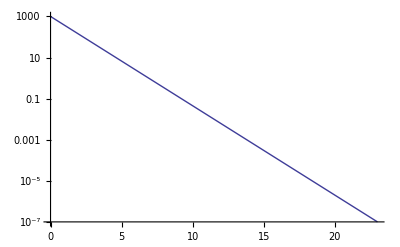

```mathematica
LogPlot[1000*E^(-x),{x,0,8}]
LogPlot[1000*E^(-x),{x,0,23}]
```

```mathematica
NSolve[1000*E^(-i*21.5)==1,i]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{i→0.321291}}

```mathematica
D[1000*E^(-x),x]/(1000*E^(-x))*1/(365*24*3600.)
Mortality/.{M->10^1}
ConsumerGrowth/.{M->10^1}
```

-3.17098×10^-8

7.50435×10^-6

2.20234×10^-7

```mathematica
D[1000*E^(-0.321*x),x]/(1000*E^(-0.321*x))*1/(365*24*3600.)
Mortality/.{M->10^5}
ConsumerGrowth/.{M->10^5}
```

-1.01788×10^-8

5.99886×10^-7

2.09997×10^-8

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->(ConsumerGrowth-i*(2*10^(-8))),μ->(Mortality+i*(2*10^(-8))),β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

```mathematica
dimH/.{i->.01,M->10^5}
```

0.00370281

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"];
```

```mathematica
Hvariations={};
Fvariations={};
HFvariations={};
Do[

Hforplt=dimH/.{i->j};
Fforplt=dimF/.{i->j};


Hvariations=Append[Hvariations,LogLogPlot[Hforplt/M,{M,1,10^12},PlotStyle->Hue[j/2]]];
Fvariations=Append[Fvariations,LogLogPlot[Fforplt/M,{M,1,10^12},PlotStyle->Hue[j/2]]];
HFvariations=Append[HFvariations,LogLogPlot[(Hforplt+Fforplt)/M,{M,1,10^12},PlotStyle->Hue[j/2]]]
,
{j,0,1,.1}
]
```

```mathematica
dataplt=ListLogLogPlot[data,PlotRange->{{1,10^12},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}];
```

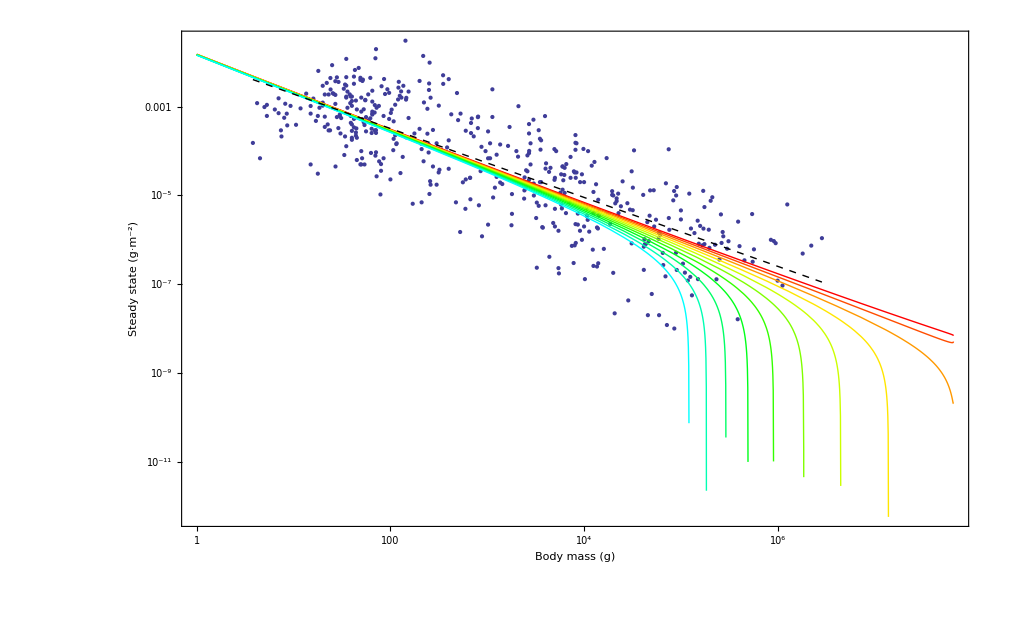

```mathematica
Show[dataplt,Fvariations,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],PlotRange->All]
```

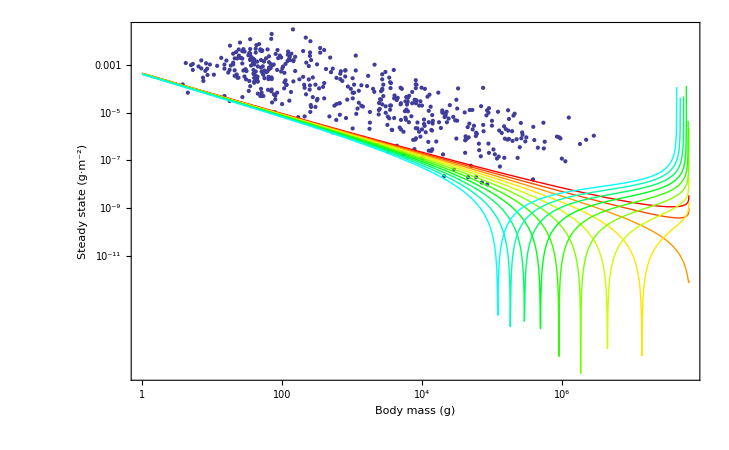

```mathematica
Show[dataplt,Hvariations,PlotRange->All]
```

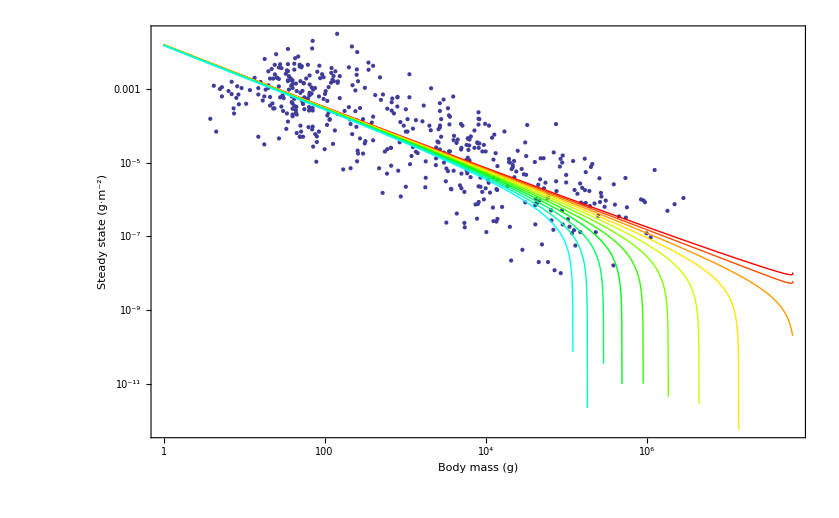

```mathematica
Show[dataplt,HFvariations,PlotRange->All]
```

Energy equivalence hypothesis

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"];
```

```mathematica
Mean[data[[All,2]]]
```

0.000791639

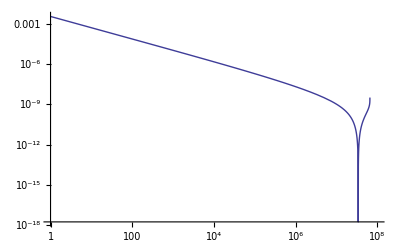

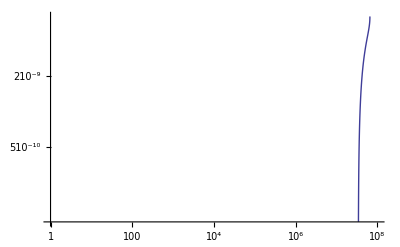

```mathematica
LogLogPlot[dimH/M,{M,1,10^8}]
LogLogPlot[dimF/M,{M,1,10^8}]
```

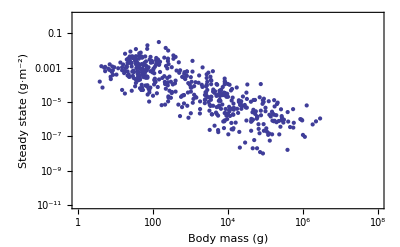

```mathematica
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}]
```

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

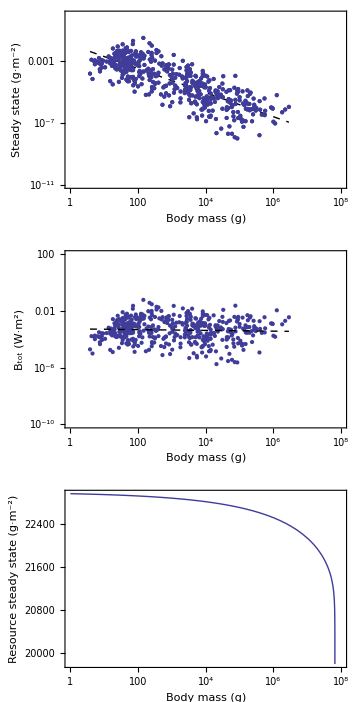

```mathematica
Cplot=GraphicsGrid[{{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,1,10^8},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,1,10^8},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
},{
Show[{
ListLogLogPlot[Table[{data[[i]][[1]],data[[i]][[2]]*(data[[i]][[1]])^(3/4)*B0},{i,Length[data]}],PlotRange->{{1,10^8},{10^-10,100}},Frame->True,FrameLabel->{"Body mass (g)","B_tot (W·m^2)"}],
LogLogPlot[0.0115643*M^(-0.776818)*M^(3/4)*B0,{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
LogLogPlot[{dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0},{M,1,10^8},Frame->True,FrameLabel->{"Body mass (g)","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]}]
},{
LogLinearPlot[dimR,{M,1,10^8},Frame->True,PlotRange->All,FrameLabel->{"Body mass (g)","Resource steady state (g·m^-2)"}]
}}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf"}],Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf

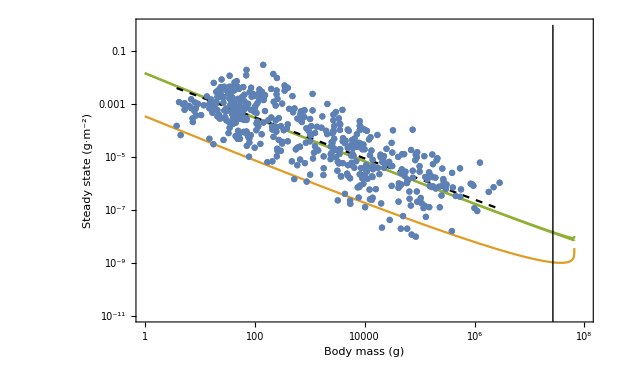

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,1,10^8},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,1,10^8},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data],
Graphics[Line[{{Log@(2.66312453830273*^7),Log@(10^-15)},{Log@(2.66312453830273*^7),Log@(1)}}]]
}]
```

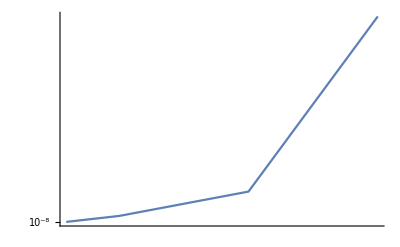

```mathematica
LogLogPlot[dimH/M+dimF/M,{M,5*10^7,10^8},PlotRange->{10^-8,All}]
```

```mathematica
Solve[f0*M^γ/M==1,M]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{M→8.30239×10^8}}

```mathematica
FindMinimum[dimR,M]
```

FindMinimum::nrnum: The function value 8380.71+288.78 ⅈ is not a real number at {M} = {2.08076×10^8}.

{8702.7,{M→1.8916×10^7}}

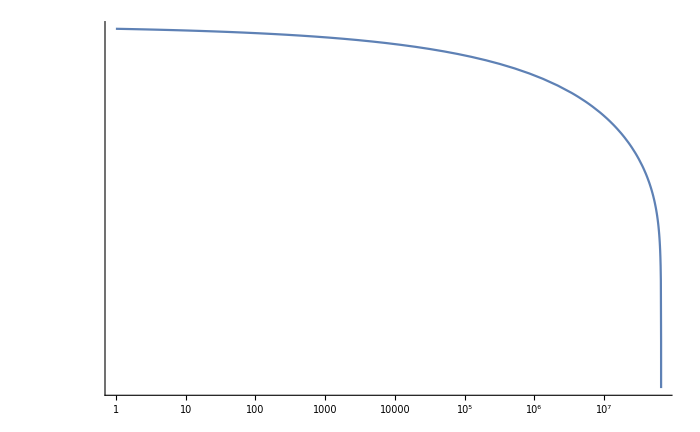

```mathematica
LogLogPlot[dimR,{M,1,10^10},PlotRange->{1000,All}]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}

```mathematica
Reduce[0.95*(1+chi)<1]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

chi<0.0526316